```mathematica
distribution::usage="Get the wavefunction of a n-step quantum walk";
distribution[plotmax_Integer,initialangle_,initialphase_,theta_,phase_]:=
Module[{n=plotmax,iangle=initialangle,iphase=initialphase,lattice,temp,rotation,δtheta},
lattice=Table[0,{i,n+1},{j,n+1},{k,2}];
temp=Table[0,{j,n+1},{k,2}];
rotation=Table[{{1,0},{0,Exp[ⅈ*phase[[i]]]}}.N[MatrixExp[-ⅈ 2 PauliMatrix[2] (theta[[i]])].PauliMatrix[3]],{i,Length[theta]}];(*Defining phase gate and coin-filp operator for each time step*)
lattice[[1,1,1]]=N[Cos[iangle]];
lattice[[1,1,2]]=N[Exp[ⅈ*iphase]* Sin[iangle]];(*Initial localized state*)
For[t=1,t≤n,t++,
For[i=1,i≤t,i++,
temp[[i,All]]=rotation[[t]].lattice[[t,i,All]];];
For[i=1,i≤t,i++,
lattice[[t+1,i,1]]=temp[[i,1]];
lattice[[t+1,i+1,2]]=temp[[i,2]];]; (*Conditional shift operator*)
];
Last[lattice]
];
GlobalState::usage="Get the density matrix of a n-step quantum walk";
GlobalState[plotmax_Integer,initialangle_,initialphase_,theta_,phase_]:=Module[{n=plotmax,iangle=initialangle,iphase=initialphase,temp,sitebase,globalstate,rho},
temp=distribution[n,iangle,iphase,theta,phase];
sitebase=DiagonalMatrix[Table[1,{i,Length[temp]}]];
globalstate=Sum[KroneckerProduct[{temp[[i]]},{sitebase[[i]]}],{i,Length[temp]}];
rho=Partition[globalstate[[1]],1].Partition[globalstate[[1]],1]†
];
```

Hadamard Quantum Walk (Green solid line in Fig.3A)

```mathematica
step=1; (*The number of discrete QW step*)
spinbase=DiagonalMatrix[Table[1,{i,2}]]; (*The reference base in the coin space*)
sitebase=DiagonalMatrix[Table[1,{i,step+1}]]; (*The reference base in the lattice space*)
refbase=Partition[Flatten[Table[KroneckerProduct[{spinbase[[i]]},{sitebase[[j]]}],{i,2},{j,step+1}]],2(step+1)]; (*The reference base in the coin+lattice space*)
projbase=Partition[Partition[Flatten[Join[refbase,Table[{Table[KroneckerProduct[{spinbase[[1]]},{sitebase[[j]]}]/√2+ⅈ*KroneckerProduct[{spinbase[[2]]},{sitebase[[Mod[j+i,step+1,1]]]}]/√2,{j,Length[sitebase]}],Table[KroneckerProduct[{spinbase[[1]]},{sitebase[[j]]}]/√2-ⅈ*KroneckerProduct[{spinbase[[2]]},{sitebase[[Mod[j+i,step+1,1]]]}]/√2,{j,Length[sitebase]}],Table[KroneckerProduct[{spinbase[[1]]},{sitebase[[j]]}]/√2+1*KroneckerProduct[{spinbase[[2]]},{sitebase[[Mod[j+i,step+1,1]]]}]/√2,{j,Length[sitebase]}],Table[KroneckerProduct[{spinbase[[1]]},{sitebase[[j]]}]/√2-1*KroneckerProduct[{spinbase[[2]]},{sitebase[[Mod[j+i,step+1,1]]]}]/√2,{j,Length[sitebase]}]},{i,0,step}]]],2(step+1)],2(step+1)];(*The measurement bases {|v^n>}(n=0,2,...,2(step+1))*)
projector=Table[Partition[projbase[[i,j]],1].Partition[projbase[[i,j]],1]†,{i,Length[projbase]},{j,Length[projbase[[i]]]}];
Table[Print["The ensmble of projectors with n=",i-1," is: ",Table[projector[[i,j]]//MatrixForm,{j,Length[projector[[1]]]}]],{i,Length[projector]}];

iangle=π/4;(*Initial state -Graphics-*)
iphase=π/2;(*Initial state -Graphics-*)
theta=Table[π/8,{i,step}];(*Hadamard gate for each discrete step*)
phase=Table[0,{i,step}];(*without introducing the phase gate*)
rhoth=GlobalState[step,iangle,iphase,theta,phase];(*The time-evolving density matrix*)
Print["The synthetic datasets  (n=0,2,...,2(step+1)) are: ",prob=Table[Re[Tr[projector[[i,j]].rhoth]],{i,Length[projbase]},{j,Length[projbase[[i]]]}]];

oper=Table[0,{i,Length[projbase]}];
Table[oper[[i]]=Sum[KroneckerProduct[projbase[[1]][[j]],Conjugate[projbase[[i]][[j]]]],{j,Length[projbase[[i]]]}],{i,Length[projbase]}];(*The base transformation matrix -Graphics- (n=0,2,...,2(step+1))*)

traindata=Join[{{2(step+1)}},{{2(step+1)+1}},N[Partition[Flatten[Table[{prob[[i]],Re[oper[[i]]],Im[oper[[i]]]},{i,Length[prob]}]],4*step/2+2]]]; (*Generate a data format that satisfies the ``Fortran'' code to train the neural network*)
```

The ensmble of projectors with n=0 is: {(1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1)}

The ensmble of projectors with n=1 is: {(1/2 | 0 | -ⅈ/2 | 0
0 | 0 | 0 | 0
ⅈ/2 | 0 | 1/2 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 1/2 | 0 | -ⅈ/2
0 | 0 | 0 | 0
0 | ⅈ/2 | 0 | 1/2),(1/2 | 0 | ⅈ/2 | 0
0 | 0 | 0 | 0
-ⅈ/2 | 0 | 1/2 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 1/2 | 0 | ⅈ/2
0 | 0 | 0 | 0
0 | -ⅈ/2 | 0 | 1/2)}

The ensmble of projectors with n=2 is: {(1/2 | 0 | 1/2 | 0
0 | 0 | 0 | 0
1/2 | 0 | 1/2 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 1/2 | 0 | 1/2
0 | 0 | 0 | 0
0 | 1/2 | 0 | 1/2),(1/2 | 0 | -1/2 | 0
0 | 0 | 0 | 0
-1/2 | 0 | 1/2 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 1/2 | 0 | -1/2
0 | 0 | 0 | 0
0 | -1/2 | 0 | 1/2)}

The ensmble of projectors with n=3 is: {(1/2 | 0 | 0 | -ⅈ/2
0 | 0 | 0 | 0
0 | 0 | 0 | 0
ⅈ/2 | 0 | 0 | 1/2),(0 | 0 | 0 | 0
0 | 1/2 | -ⅈ/2 | 0
0 | ⅈ/2 | 1/2 | 0
0 | 0 | 0 | 0),(1/2 | 0 | 0 | ⅈ/2
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-ⅈ/2 | 0 | 0 | 1/2),(0 | 0 | 0 | 0
0 | 1/2 | ⅈ/2 | 0
0 | -ⅈ/2 | 1/2 | 0
0 | 0 | 0 | 0)}

The ensmble of projectors with n=4 is: {(1/2 | 0 | 0 | 1/2
0 | 0 | 0 | 0
0 | 0 | 0 | 0
1/2 | 0 | 0 | 1/2),(0 | 0 | 0 | 0
0 | 1/2 | 1/2 | 0
0 | 1/2 | 1/2 | 0
0 | 0 | 0 | 0),(1/2 | 0 | 0 | -1/2
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-1/2 | 0 | 0 | 1/2),(0 | 0 | 0 | 0
0 | 1/2 | -1/2 | 0
0 | -1/2 | 1/2 | 0
0 | 0 | 0 | 0)}

The synthetic datasets … (n=0,2,...,2(step+1)) are: {{0.5,0.,0.,0.5},{0.25,0.25,0.25,0.25},{0.25,0.25,0.25,0.25},{0.,0.,1.,0.},{0.5,0.,0.5,0.}}

```mathematica
figRE=BarChart3D[Re[rhoth],Axes->{True,True,True},Ticks->{None,None,None},TicksStyle->Directive[18,FontFamily->"Arial"],FaceGrids->{{0,1,0},{0,0,-1},{-1,0,0}},PlotRange->{-1,1},FaceGridsStyle->Directive[{Gray,Thickness[0.005]}],ChartLayout->"Grid",AxesStyle->Thickness[0.005],BarSpacing->{0.5,0.5},BoxRatios->{2,2,1.5},ViewPoint->{2,-3,2},ChartStyle->"Rainbow",Method->{"Canvas"->None},AxesStyle->Directive[FontSize->15],ImageSize->200];
Print["Visualizing the real part of density matrix: ",figRE]
figIm=BarChart3D[Im[rhoth],Axes->{True,True,True},Ticks->{None,None,None},TicksStyle->Directive[18,FontFamily->"Arial"],FaceGrids->{{0,1,0},{0,0,-1},{-1,0,0}},PlotRange->{-1,1},FaceGridsStyle->Directive[{Gray,Thickness[0.005]}],ChartLayout->"Grid",AxesStyle->Thickness[0.005],BarSpacing->{0.5,0.5},BoxRatios->{2,2,1.5},ViewPoint->{2,-3,2},ChartStyle->"Rainbow",Method->{"Canvas"->None},AxesStyle->Directive[FontSize->15],ImageSize->200];
Print["Visualizing the imaginary part of density matrix: ",figIm]
```

Visualizing the real part of density matrix: -Graphics3D-

Visualizing the imaginary part of density matrix: -Graphics3D-

Coherent Disordered Quantum Walk (red dashed line in Fig.3A)

```mathematica
step=2; (*The number of discrete QW step*)
spinbase=DiagonalMatrix[Table[1,{i,2}]]; (*The reference base in the coin space*)
sitebase=DiagonalMatrix[Table[1,{i,step+1}]]; (*The reference base in the lattice space*)
refbase=Partition[Flatten[Table[KroneckerProduct[{spinbase[[i]]},{sitebase[[j]]}],{i,2},{j,step+1}]],2(step+1)]; (*The reference base in the coin+lattice space*)
projbase=Partition[Partition[Flatten[Join[refbase,Table[{Table[KroneckerProduct[{spinbase[[1]]},{sitebase[[j]]}]/√2+ⅈ*KroneckerProduct[{spinbase[[2]]},{sitebase[[Mod[j+i,step+1,1]]]}]/√2,{j,Length[sitebase]}],Table[KroneckerProduct[{spinbase[[1]]},{sitebase[[j]]}]/√2-ⅈ*KroneckerProduct[{spinbase[[2]]},{sitebase[[Mod[j+i,step+1,1]]]}]/√2,{j,Length[sitebase]}],Table[KroneckerProduct[{spinbase[[1]]},{sitebase[[j]]}]/√2+1*KroneckerProduct[{spinbase[[2]]},{sitebase[[Mod[j+i,step+1,1]]]}]/√2,{j,Length[sitebase]}],Table[KroneckerProduct[{spinbase[[1]]},{sitebase[[j]]}]/√2-1*KroneckerProduct[{spinbase[[2]]},{sitebase[[Mod[j+i,step+1,1]]]}]/√2,{j,Length[sitebase]}]},{i,0,step}]]],2(step+1)],2(step+1)];(*The measurement bases {|v^n>}(n=1,2,...,2(step+1)+1)*)
projector=Table[Partition[projbase[[i,j]],1].Partition[projbase[[i,j]],1]†,{i,Length[projbase]},{j,Length[projbase[[i]]]}];
(*Table[Print["The ensmble of projectors with n=",i," is: ",Table[projector[[i,j]]//MatrixForm,{j,Length[projector[[1]]]}]],{i,Length[projector]}];*)

iangle=π/4;(*Initial state -Graphics-*)
iphase=π/2;(*Initial state -Graphics-*)

sample=100; (*Choose the number of samples*)
traindata=Table[0,{i,sample}];(*sample size*)
rhoth=Table[0,{i,sample}];
For[s=1,s≤sample,s++,
theta=RandomReal[{0,π/2},step];(*The coin-filp angle becomes completely random for each time step*)
phase=Table[0,{i,step}];(*without introducing the phase gate*)

rhoth[[s]]=GlobalState[step,iangle,iphase,theta,phase];(*The time-evolving density matrix*)
prob=Table[Re[Tr[projector[[i,j]].rhoth[[s]]]],{i,Length[projbase]},{j,Length[projbase[[i]]]}];(*The synthetic datasets -Graphics- (n=1,2,...,2(step+1)+1)*)

oper=Table[0,{i,Length[projbase]}];
Table[oper[[i]]=Sum[KroneckerProduct[projbase[[1]][[j]],Conjugate[projbase[[i]][[j]]]],{j,Length[projbase[[i]]]}],{i,Length[projbase]}];(*The base transformation matrix -Graphics- (n=1,2,...,2(step+1)+1)*)

traindata[[s]]=Join[{{2(step+1)}},{{2(step+1)+1}},N[Partition[Flatten[Table[{prob[[i]],Re[oper[[i]]],Im[oper[[i]]]},{i,Length[prob]}]],4*step/2+2]]];(*Generate a data format that satisfies the ``Fortran'' code to train the neural network*)
]
```

```mathematica
figRE=BarChart3D[Re[rhoth[[100]]],Axes->{True,True,True},Ticks->{None,None,None},TicksStyle->Directive[18,FontFamily->"Arial"],FaceGrids->{{0,1,0},{0,0,-1},{-1,0,0}},PlotRange->{-1,1},FaceGridsStyle->Directive[{Gray,Thickness[0.005]}],ChartLayout->"Grid",AxesStyle->Thickness[0.005],BarSpacing->{0.5,0.5},BoxRatios->{2,2,1.5},ViewPoint->{2,-3,2},ChartStyle->"Rainbow",Method->{"Canvas"->None},AxesStyle->Directive[FontSize->15],ImageSize->200];
Print["Visualizing the real part of density matrix (sample=1): ",figRE]
figIm=BarChart3D[Im[rhoth[[100]]],Axes->{True,True,True},Ticks->{None,None,None},TicksStyle->Directive[18,FontFamily->"Arial"],FaceGrids->{{0,1,0},{0,0,-1},{-1,0,0}},PlotRange->{-1,1},FaceGridsStyle->Directive[{Gray,Thickness[0.005]}],ChartLayout->"Grid",AxesStyle->Thickness[0.005],BarSpacing->{0.5,0.5},BoxRatios->{2,2,1.5},ViewPoint->{2,-3,2},ChartStyle->"Rainbow",Method->{"Canvas"->None},AxesStyle->Directive[FontSize->15],ImageSize->200];
Print["Visualizing the imaginary part of density matrix: ",figIm]
```

Visualizing the real part of density matrix (sample=1): -Graphics3D-

Visualizing the imaginary part of density matrix: -Graphics3D-

Open Quantum Walk with the phase decoherence of the coin (blue dash-dotted line in Fig.3B and blue solid line in Fig.4A)

```mathematica
step=5; (*The number of discrete QW step*)
spinbase=DiagonalMatrix[Table[1,{i,2}]]; (*The reference base in the coin space*)
sitebase=DiagonalMatrix[Table[1,{i,step+1}]]; (*The reference base in the lattice space*)
refbase=Partition[Flatten[Table[KroneckerProduct[{spinbase[[i]]},{sitebase[[j]]}],{i,2},{j,step+1}]],2(step+1)]; (*The reference base in the coin+lattice space*)
projbase=Partition[Partition[Flatten[Join[refbase,Table[{Table[KroneckerProduct[{spinbase[[1]]},{sitebase[[j]]}]/√2+ⅈ*KroneckerProduct[{spinbase[[2]]},{sitebase[[Mod[j+i,step+1,1]]]}]/√2,{j,Length[sitebase]}],Table[KroneckerProduct[{spinbase[[1]]},{sitebase[[j]]}]/√2-ⅈ*KroneckerProduct[{spinbase[[2]]},{sitebase[[Mod[j+i,step+1,1]]]}]/√2,{j,Length[sitebase]}],Table[KroneckerProduct[{spinbase[[1]]},{sitebase[[j]]}]/√2+1*KroneckerProduct[{spinbase[[2]]},{sitebase[[Mod[j+i,step+1,1]]]}]/√2,{j,Length[sitebase]}],Table[KroneckerProduct[{spinbase[[1]]},{sitebase[[j]]}]/√2-1*KroneckerProduct[{spinbase[[2]]},{sitebase[[Mod[j+i,step+1,1]]]}]/√2,{j,Length[sitebase]}]},{i,0,step}]]],2(step+1)],2(step+1)];(*The measurement bases {|v^n>}(n=1,2,...,2(step+1)+1)*)
projector=Table[Partition[projbase[[i,j]],1].Partition[projbase[[i,j]],1]†,{i,Length[projbase]},{j,Length[projbase[[i]]]}];
(*Table[Print["The ensmble of projectors with n=",i," is: ",Table[projector[[i,j]]//MatrixForm,{j,Length[projector[[1]]]}]],{i,Length[projector]}];*)

iangle=π/4;(*Initial state -Graphics-*)
iphase=π/2;(*Initial state -Graphics-*)

deltabeta=Table[i,{i,0,π,π/100}];(*choose different values of the fluctuating degree*)
sample=Length[deltabeta]; (*The number of samples*)

traindata=Table[0,{i,sample}];(*sample size*)
rhoth=Table[0,{i,sample}];
purity=Table[0,{i,sample}];

For[s=1,s≤sample,s++,
theta=Table[π/8,{i,step}];(*Hadamard gate for each discrete step*)
(*theta=RandomReal[{0,π/2},step];(*The coin-filp angle becomes completely random for each time step*)*)

trialnumber=1000;(*Set the number of trials*)
phase=Table[Table[RandomReal[{-deltabeta[[s]],deltabeta[[s]]}],{i,step}],{j,trialnumber}];(*Introducing the random phase gate*)

rhoth[[s]]=Total[Table[GlobalState[step,iangle,iphase,theta,phase[[i]]],{i,trialnumber}]]/trialnumber;(*The ensemble-averaged density matrix *)
purity[[s]]={deltabeta[[s]],Re[Tr[rhoth[[s]].rhoth[[s]]]]};

prob=Table[Re[Tr[projector[[i,j]].rhoth[[s]]]],{i,Length[projbase]},{j,Length[projbase[[i]]]}];(*The synthetic datasets -Graphics- (n=1,2,...,2(step+1)+1)*)

oper=Table[0,{i,Length[projbase]}];
Table[oper[[i]]=Sum[KroneckerProduct[projbase[[1]][[j]],Conjugate[projbase[[i]][[j]]]],{j,Length[projbase[[i]]]}],{i,Length[projbase]}];(*The base transformation matrix -Graphics- (n=1,2,...,2(step+1)+1)*)

traindata[[s]]=Join[{{2(step+1)}},{{2(step+1)+1}},N[Partition[Flatten[Table[{prob[[i]],Re[oper[[i]]],Im[oper[[i]]]},{i,Length[prob]}]],4*step/2+2]]];(*Generate a data format that satisfies the ``Fortran'' code to train the neural network*)
]
```

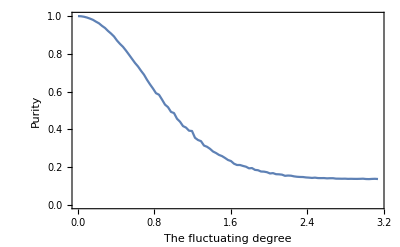

```mathematica
ListLinePlot[purity,PlotRange->All,Frame->{{True,True},{True,True}},FrameLabel->{"The fluctuating degree","Purity"},LabelStyle->Directive[Black,16],ImageSize->400]
```

Open Quantum Walk with depolarizing noise (Fig.S1 in supplementary materials)

```mathematica
step=5; (*The number of discrete QW step*)
spinbase=DiagonalMatrix[Table[1,{i,2}]]; (*The reference base in the coin space*)
sitebase=DiagonalMatrix[Table[1,{i,step+1}]]; (*The reference base in the lattice space*)
refbase=Partition[Flatten[Table[KroneckerProduct[{spinbase[[i]]},{sitebase[[j]]}],{i,2},{j,step+1}]],2(step+1)]; (*The reference base in the coin+lattice space*)
projbase=Partition[Partition[Flatten[Join[refbase,Table[{Table[KroneckerProduct[{spinbase[[1]]},{sitebase[[j]]}]/√2+ⅈ*KroneckerProduct[{spinbase[[2]]},{sitebase[[Mod[j+i,step+1,1]]]}]/√2,{j,Length[sitebase]}],Table[KroneckerProduct[{spinbase[[1]]},{sitebase[[j]]}]/√2-ⅈ*KroneckerProduct[{spinbase[[2]]},{sitebase[[Mod[j+i,step+1,1]]]}]/√2,{j,Length[sitebase]}],Table[KroneckerProduct[{spinbase[[1]]},{sitebase[[j]]}]/√2+1*KroneckerProduct[{spinbase[[2]]},{sitebase[[Mod[j+i,step+1,1]]]}]/√2,{j,Length[sitebase]}],Table[KroneckerProduct[{spinbase[[1]]},{sitebase[[j]]}]/√2-1*KroneckerProduct[{spinbase[[2]]},{sitebase[[Mod[j+i,step+1,1]]]}]/√2,{j,Length[sitebase]}]},{i,0,step}]]],2(step+1)],2(step+1)];(*The measurement bases {|v^n>}(n=1,2,...,2(step+1)+1)*)
projector=Table[Partition[projbase[[i,j]],1].Partition[projbase[[i,j]],1]†,{i,Length[projbase]},{j,Length[projbase[[i]]]}];
(*Table[Print["The ensmble of projectors with n=",i," is: ",Table[projector[[i,j]]//MatrixForm,{j,Length[projector[[1]]]}]],{i,Length[projector]}];*)

iangle=π/4;(*Initial state -Graphics-*)
iphase=π/2;(*Initial state -Graphics-*)
pde=Table[i,{i,0,1,1/100.}];(*choose different depolarizing noise strengths*)

sample=Length[pde]; (*The number of samples*)
traindata=Table[0,{i,sample}];(*sample size*)
rhoth=Table[0,{i,sample}];
purity=Table[0,{i,sample}];
For[s=1,s≤sample,s++,
theta=RandomReal[{0,π/2},step];(*The coin-filp angle becomes completely random for each time step*)
phase=Table[0,{i,step}];(*without introducing the phase gate*)
rhothe=GlobalState[step,iangle,iphase,theta,phase];
rhoth[[s]]=(1-pde[[s]])*rhothe+pde[[s]]*IdentityMatrix[2(step+1)]/(2(step+1));(*The depolarizing density matrix *)
purity[[s]]={pde[[s]],Re[Tr[rhoth[[s]].rhoth[[s]]]]};
prob=Table[Re[Tr[projector[[i,j]].rhoth[[s]]]],{i,Length[projbase]},{j,Length[projbase[[i]]]}];(*The synthetic datasets -Graphics- (n=1,2,...,2(step+1)+1)*)

oper=Table[0,{i,Length[projbase]}];
Table[oper[[i]]=Sum[KroneckerProduct[projbase[[1]][[j]],Conjugate[projbase[[i]][[j]]]],{j,Length[projbase[[i]]]}],{i,Length[projbase]}];(*The base transformation matrix -Graphics- (n=1,2,...,2(step+1)+1)*)

traindata[[s]]=Join[{{2(step+1)}},{{2(step+1)+1}},N[Partition[Flatten[Table[{prob[[i]],Re[oper[[i]]],Im[oper[[i]]]},{i,Length[prob]}]],4*step/2+2]]];(*Generate a data format that satisfies the ``Fortran'' code to train the neural network*)
]
```

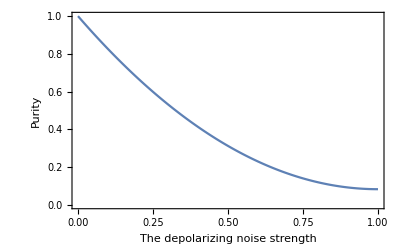

```mathematica
ListLinePlot[purity,PlotRange->All,Frame->{{True,True},{True,True}},FrameLabel->{"The depolarizing noise strength","Purity"},LabelStyle->Directive[Black,16],ImageSize->400]
```

```mathematica
fig1=BarChart3D[Re[rhoth[[101]]],Axes->{True,True,True},Ticks->{None,None,None},TicksStyle->Directive[18,FontFamily->"Arial"],FaceGrids->{{0,1,0},{0,0,-1},{-1,0,0}},PlotRange->{-0.3,0.3},FaceGridsStyle->Directive[{Gray,Thickness[0.005]}],ChartLayout->"Grid",AxesStyle->Thickness[0.005],BarSpacing->{0.5,0.5},BoxRatios->{2,2,1.5},ViewPoint->{2,-3,2},ChartStyle->"Rainbow",Method->{"Canvas"->None},AxesStyle->Directive[FontSize->15],ImageSize->300]
fig2=BarChart3D[Im[rhoth[[101]]],Axes->{True,True,True},Ticks->{None,None,None},TicksStyle->Directive[18,FontFamily->"Arial"],FaceGrids->{{0,1,0},{0,0,-1},{-1,0,0}},PlotRange->{-0.3,0.3},FaceGridsStyle->Directive[{Gray,Thickness[0.005]}],ChartLayout->"Grid",AxesStyle->Thickness[0.005],BarSpacing->{0.5,0.5},BoxRatios->{2,2,1.5},ViewPoint->{2,-3,2},ChartStyle->"Rainbow",Method->{"Canvas"->None},AxesStyle->Directive[FontSize->15],ImageSize->300]
```

-Graphics3D-

-Graphics3D-

Open Quantum Walk with measuremnts both in the coin and the lattice space  (Fig.S2 in supplementary materials)

```mathematica
step=5;

spinbase=DiagonalMatrix[Table[1,{i,2}]];
sitebase=DiagonalMatrix[Table[1,{i,step+1}]];

w=Table[i,{i,0.,1.0,1.0/100}];(* Choose different mixing parameter*)
ws=wl=Table[w[[i]]/2,{i,Length[w]}];(*Set ws=wl*)
w0=Table[1-w[[i]],{i,Length[w]}];

purity=Table[0,{i,Length[w]}];
rhoth=Table[0,{i,Length[w]}];
data=Table[0,{i,Length[w]}];
prob=Table[0,{i,Length[w]}];

For[sample=1,sample≤Length[w],sample++,

initial=Flatten[KroneckerProduct[{1./Sqrt[2],ⅈ/Sqrt[2]},sitebase[[1]]]];(*Initial state -Graphics-*)
rhoini=Partition[initial,1].Partition[initial,1]†;

coin=KroneckerProduct[HadamardMatrix[2],sitebase];(*Set Hadamard as the coin-flip operator*)

shift=Table[0,{i,2(step+1)},{j,2(step+1)}];
Table[shift[[i,i]]=1,{i,step+1}];
Table[shift[[i+step+2,i+step+1]]=1,{i,step}];(*Define the shift operator*)

pc=Table[Total[Table[Partition[Flatten[KroneckerProduct[spinbase[[c]],sitebase[[x]]]],1].Partition[Flatten[KroneckerProduct[spinbase[[c]],sitebase[[x]]]],1]†,{x,step+1}]],{c,2}];(*Define the projector *)
pl=Table[Total[Table[Partition[Flatten[KroneckerProduct[spinbase[[c]],sitebase[[x]]]],1].Partition[Flatten[KroneckerProduct[spinbase[[c]],sitebase[[x]]]],1]†,{c,2}]],{x,step+1}];(*Define the projector *)


rhothe=Table[0,{i,step+1}];
rhothe[[1]]=rhoini;
For[k=1,k≤step,k++,
rhothe[[k+1]]=w0[[sample]]*((shift.coin).rhothe[[k]].(shift.coin)†)+ws[[sample]]*Total[Table[(pc[[c]].shift.coin).rhothe[[k]].(pc[[c]].shift.coin)†,{c,2}]]+wl[[sample]]*Total[Table[(pl[[x]].shift.coin).rhothe[[k]].(pl[[x]].shift.coin)†,{x,Length[pl]}]];
];(*The time-evolving density matrix *)
rhoth[[sample]]=rhothe[[step+1]];
purity[[sample]]={w[[sample]],Re[Tr[rhoth[[sample]].rhoth[[sample]]]]};
]
```

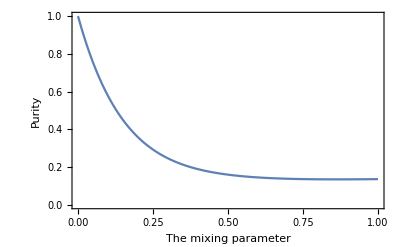

```mathematica
ListLinePlot[purity,PlotRange->All,Frame->{{True,True},{True,True}},FrameLabel->{"The mixing parameter","Purity"},LabelStyle->Directive[Black,16],ImageSize->400]
```

```mathematica
fig1=BarChart3D[Re[rhoth[[101]]],Axes->{True,True,True},Ticks->{None,None,None},TicksStyle->Directive[18,FontFamily->"Arial"],FaceGrids->{{0,1,0},{0,0,-1},{-1,0,0}},PlotRange->{-0.3,0.3},FaceGridsStyle->Directive[{Gray,Thickness[0.005]}],ChartLayout->"Grid",AxesStyle->Thickness[0.005],BarSpacing->{0.5,0.5},BoxRatios->{2,2,1.5},ViewPoint->{2,-3,2},ChartStyle->"Rainbow",Method->{"Canvas"->None},AxesStyle->Directive[FontSize->15],ImageSize->300]
fig2=BarChart3D[Im[rhoth[[101]]],Axes->{True,True,True},Ticks->{None,None,None},TicksStyle->Directive[18,FontFamily->"Arial"],FaceGrids->{{0,1,0},{0,0,-1},{-1,0,0}},PlotRange->{-0.3,0.3},FaceGridsStyle->Directive[{Gray,Thickness[0.005]}],ChartLayout->"Grid",AxesStyle->Thickness[0.005],BarSpacing->{0.5,0.5},BoxRatios->{2,2,1.5},ViewPoint->{2,-3,2},ChartStyle->"Rainbow",Method->{"Canvas"->None},AxesStyle->Directive[FontSize->15],ImageSize->300]
```

-Graphics3D-

-Graphics3D-